# How Do I Mathematica?

## by Kush Patel

# Module 4 - Graphics

## 4.1 Basic Graphics

Mathematica can generate graphics as simple or complex as you want. The function is Graphics[] and this will plot a series of Primitives that Mathematica already provides. Such primitives include Circle, Line, and Rectangle. Use the documentation to see how

### Graphing Primitives

This simple command will draw a basic unit circle.



```mathematica
Graphics[Circle[]]
```

Notice, Circle itself is a function. Supplying no parameters will generate just a unit circle. Or, you can input some parameters and get different results out.

```mathematica
Circle[{x,y}]
```

will create a unit circle centered at (x,y). However, Mathematica will intelligently recenter and rescale your graphic around what it thinks gives the best viewpoint. Therefore, it looks identical to the circle above.

```mathematica
Graphics[Circle[{2,1}]]
```

-Graphics-

If we turn on the Axes, we can see that it is, in fact, shifted.

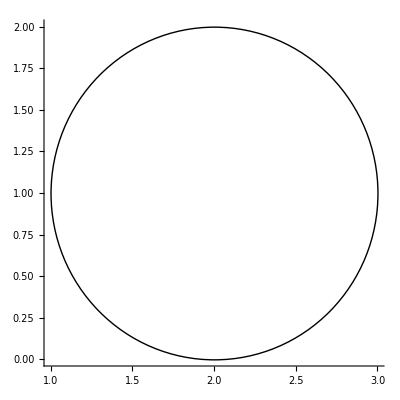

```mathematica
Graphics[Circle[{2,1}],Axes->True]
```

You can also define the PlotRange, much like you could in Plot.

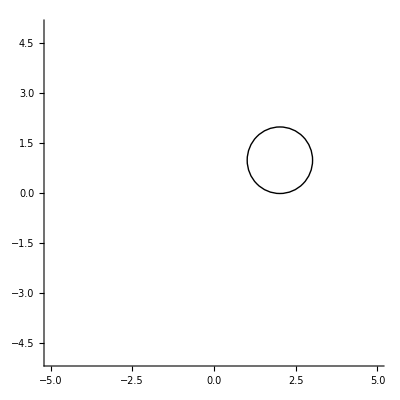

```mathematica
Graphics[Circle[{2,1}],Axes->True,PlotRange->{{-5,5},{-5,5}}]
```

You can change the radius of the circle.

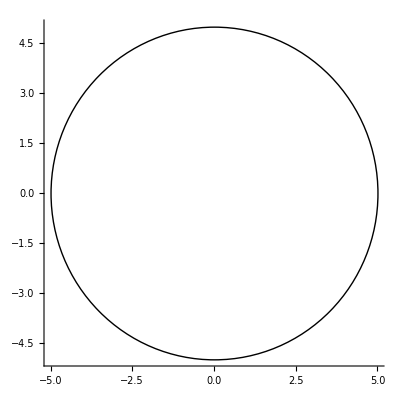

```mathematica
Graphics[Circle[{0,0},5],Axes->True]
```

You can plot multiple primitives in the same graphics function.

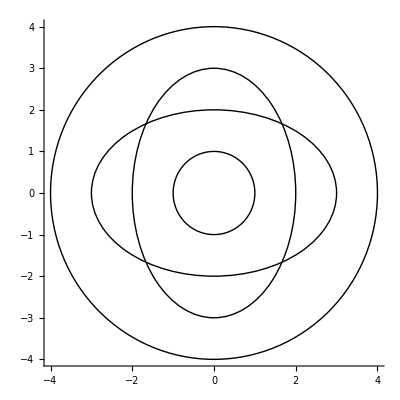

```mathematica
Graphics[{Circle[],Circle[{0,0},4],Circle[{0,0},{2,3}],Circle[{0,0},{3,2}]},Axes->True]
```

### Colors

Like Circle[], Disk[] is a primitive. This will give a filled in circle. By default, all primitives are colored black.



```mathematica
Graphics[Disk[]]
```

You can change this by simply adding a predefined color to the graphics function.



```mathematica
Graphics[{Red,Disk[]}]
```

If you graph multiple primitives, you can set each of their colors. Be careful, primitives can overlap one another.

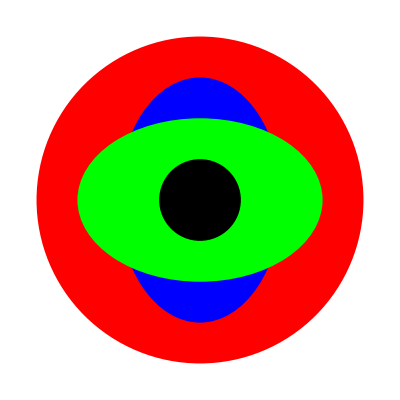

```mathematica
Graphics[{Red,Disk[{0,0},4],Blue,Disk[{0,0},{2,3}],Green,Disk[{0,0},{3,2}],Black,Disk[]}]
```

You can also define your own colors using RGB, CMYK, LAB, LCH, LUV values and more.

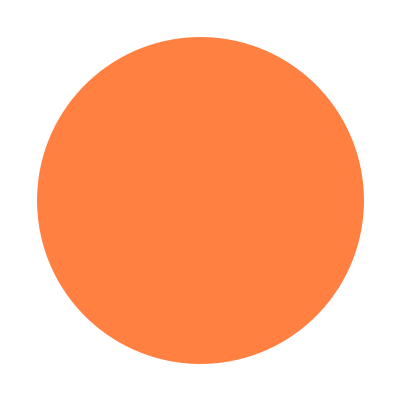

```mathematica
Graphics[{RGBColor[{1.0,0.5,0.25}],Disk[]}]
```

## 4.2 3D Graphics

You can generate 3-dimensional images using Graphics3D[]. Graphics3D has its own set of Primitives.

```mathematica
Graphics3D[Sphere[]]
```

-Graphics3D-

Most 2D Primitives will not work in Graphics3D.

```mathematica
Graphics3D[Disk[]]
```

-Graphics3D-

You can combine functions in Mathematica to quickly generate large structures.

```mathematica
lattice=Table[
Sphere[{i,j,k},0.5]
,{i,1,5},{j,1,5},{k,1,5}];
Graphics3D[lattice]
```

-Graphics3D-

Lots of room for creativity.

```mathematica
lattice2=Table[
{Hue[(i*j*k)/125],Sphere[{i,j,k},0.5]}
,{i,1,5},{j,1,5},{k,1,5}];
Graphics3D[lattice2]
```

-Graphics3D-

You can use your mouse to click and drag a 3D structure to rotate and get a full view of it.There is also a Plot3D function that will plot in the z-axis as functions of x- and y-coordinates.